```mathematica
a=0; b=6;n=4;
h=(b-a)/n;
XDT={}; YDT={};
For[i=0,i<=n,i++,
xdata[i]=a+i×h;
ydata[i]=N[xdata[i]/(√(1+xdata[i]^2+√((1+xdata[i]^2)^3)))];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];Array[ydata,{n+1,0}];
ex=∑_(i=0)^n xdata[i];ey=∑_(i=0)^n ydata[i];exx=∑_(i=0)^n xdata[i]^2;
exy=∑_(i=0)^n xdata[i]*ydata[i];
eyy=∑_(i=0)^n ydata[i]^2;
a=(ey*exx-ex*exy)/((n+1)*exx-ex^2);b=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
g[x_]:=a+b*x;
g[x]
```

0.217673+0.043762 x

```mathematica
For[i=0,i<=n,i++,xdata[i]=XDT[[i+1]];
ydata[i]=YDT[[i+1]]];
pln=∑_(i=0)^n ydata[i]*∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
```

0.+0.699911 x-0.32743 x^2+0.0603498 x^3-0.00391737 x^4

{{0.,0.},{0.6,0.349569},{1.2,0.479946},{1.8,0.499794},{2.4,0.486504},{3.,0.465003},{3.6,0.442731},{4.2,0.421868},{4.8,0.402935},{5.4,0.385918},{6.,0.370637}}

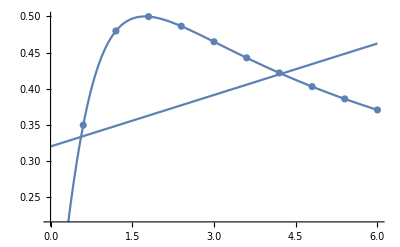

{{0.,0.694738},{0.6,2.11037},{1.2,6.85994},{1.8,19.8499},{2.4,35.5054},{3.,47.849},{3.6,51.616},{4.2,45.1195},{4.8,32.0584},{5.4,18.5322},{6.,8.71884}}

```mathematica
data=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]
Clear[a,b];rules=FindFit[data,a+b*x,{a,b,c},x];y=a+b*x/.rules;
gr1:=Plot[N[x/(√(1+x^2+√((1+x^2)^3)))],{x,0,6}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[y,{x,0,6}];
Show[{gr1,gr2,gr3}]
```

```mathematica
r=((n+1)*exy-ex*ey)/(√((n+1)*exx-ex^2)*√((n+1)*eyy-ey^2))
```

0.340156

Show::gcomb: Could not combine the graphics objects in Show[{gr1, gr2, gr3}].